```mathematica
(* Mathematica*)
```

```mathematica
(* Rubber Polyhedron polynomial in probability Bezier*)
```

```mathematica
pa[x_,p_]=ExpandAll[p*((0.9359999999999999+0.3520000000000005 ⅈ)+(7.216000000000006-6.688000000000004 ⅈ) x^2+(9.240000000000014+31.679999999999993 ⅈ) x^4+(19.359999999999985+3.519999999999956 ⅈ) x^6+(19.800000000000022-26.40000000000002 ⅈ) x^8+(4.400000000000003+8.800000000000008 ⅈ) x^10+x)+(1-p)*(x^12+14*x^6+1)]
```

1-(0.064-0.352 ⅈ) p+p x+(7.216-6.688 ⅈ) p x^2+(9.24+31.68 ⅈ) p x^4+14 x^6+(5.36+3.52 ⅈ) p x^6+(19.8-26.4 ⅈ) p x^8+(4.4+8.8 ⅈ) p x^10+x^12-p x^12

```mathematica
(* Killing vectors in probability p variable*)
```

```mathematica
d[p_]={Re[x],Im[x]}/.NSolve[pa[x,p]==0,x];
```

```mathematica
Length[d[p]]
```

12

```mathematica
dt[p_]=Transpose[d[p]];
```

```mathematica
TableForm[2*d[1/5].dt[1/5]/2.9050639651364114]
```

2. | 0.0925452 | 0.249022 | 0.696464 | -0.267938 | -0.0768786 | 0.143402 | 0.264314 | -0.718433 | -0.289792 | -0.0930574 | -1.99965
0.0925452 | 2.43 | 1.08895 | 0.0474481 | 1.45914 | 0.726856 | -0.7137 | -1.47536 | -0.0384395 | -1.09463 | -2.43015 | -0.0926661
0.249022 | 1.08895 | 0.509566 | 0.093478 | 0.620252 | 0.314855 | -0.302096 | -0.627829 | -0.0917606 | -0.516328 | -1.08907 | -0.249039
0.696464 | 0.0474481 | 0.093478 | 0.242626 | -0.0840708 | -0.0221884 | 0.0454173 | 0.0827082 | -0.250214 | -0.107699 | -0.0476273 | -0.696342
-0.267938 | 1.45914 | 0.620252 | -0.0840708 | 0.928594 | 0.453398 | -0.456197 | -0.937841 | 0.0930958 | -0.617092 | -1.45915 | 0.267807
-0.0768786 | 0.726856 | 0.314855 | -0.0221884 | 0.453398 | 0.222891 | -0.222414 | -0.45809 | 0.0260516 | -0.31443 | -0.726874 | 0.0768238
0.143402 | -0.7137 | -0.302096 | 0.0454173 | -0.456197 | -0.222414 | 0.224192 | 0.460702 | -0.0499696 | 0.300299 | 0.713701 | -0.143336
0.264314 | -1.47536 | -0.627829 | 0.0827082 | -0.937841 | -0.45809 | 0.460702 | 0.947202 | -0.0917597 | 0.624768 | 1.47537 | -0.264183
-0.718433 | -0.0384395 | -0.0917606 | -0.250214 | 0.0930958 | 0.0260516 | -0.0499696 | -0.0917597 | 0.258084 | 0.106414 | 0.0386237 | 0.718307
-0.289792 | -1.09463 | -0.516328 | -0.107699 | -0.617092 | -0.31443 | 0.300299 | 0.624768 | 0.106414 | 0.523926 | 1.09476 | 0.289802
-0.0930574 | -2.43015 | -1.08907 | -0.0476273 | -1.45915 | -0.726874 | 0.713701 | 1.47537 | 0.0386237 | 1.09476 | 2.4303 | 0.0931782
-1.99965 | -0.0926661 | -0.249039 | -0.696342 | 0.267807 | 0.0768238 | -0.143336 | -0.264183 | 0.718307 | 0.289802 | 0.0931782 | 1.9993

```mathematica
Table[TableForm[d[p].dt[p]],{p,0,9/10,1/10}]
```

{2.40602 | 1.20301 | 1. | 0.5 | -0.5 | 0.5 | 1.20301 | -1.20301 | -1. | -0.5 | -1.20301 | -2.40602
1.20301 | 2.40602 | 0.5 | 1. | 0.5 | -0.5 | -1.20301 | 1.20301 | -0.5 | -1. | -2.40602 | -1.20301
1. | 0.5 | 0.415625 | 0.207812 | -0.207812 | 0.207812 | 0.5 | -0.5 | -0.415625 | -0.207812 | -0.5 | -1.
0.5 | 1. | 0.207812 | 0.415625 | 0.207812 | -0.207812 | -0.5 | 0.5 | -0.207812 | -0.415625 | -1. | -0.5
-0.5 | 0.5 | -0.207812 | 0.207812 | 0.415625 | -0.415625 | -1. | 1. | 0.207812 | -0.207812 | -0.5 | 0.5
0.5 | -0.5 | 0.207812 | -0.207812 | -0.415625 | 0.415625 | 1. | -1. | -0.207812 | 0.207812 | 0.5 | -0.5
1.20301 | -1.20301 | 0.5 | -0.5 | -1. | 1. | 2.40602 | -2.40602 | -0.5 | 0.5 | 1.20301 | -1.20301
-1.20301 | 1.20301 | -0.5 | 0.5 | 1. | -1. | -2.40602 | 2.40602 | 0.5 | -0.5 | -1.20301 | 1.20301
-1. | -0.5 | -0.415625 | -0.207812 | 0.207812 | -0.207812 | -0.5 | 0.5 | 0.415625 | 0.207812 | 0.5 | 1.
-0.5 | -1. | -0.207812 | -0.415625 | -0.207812 | 0.207812 | 0.5 | -0.5 | 0.207812 | 0.415625 | 1. | 0.5
-1.20301 | -2.40602 | -0.5 | -1. | -0.5 | 0.5 | 1.20301 | -1.20301 | 0.5 | 1. | 2.40602 | 1.20301
-2.40602 | -1.20301 | -1. | -0.5 | 0.5 | -0.5 | -1.20301 | 1.20301 | 1. | 0.5 | 1.20301 | 2.40602,2.67999 | 0.883948 | 0.418464 | 1.00551 | -0.930709 | -0.379564 | 0.402527 | 0.930617 | -1.02277 | -0.425234 | -0.88315 | -2.67963
0.883948 | 2.44948 | 1.06622 | 0.344734 | 1.76181 | 0.742836 | -0.718828 | -1.76278 | -0.343006 | -1.09158 | -2.44886 | -0.883968
0.418464 | 1.06622 | 0.464591 | 0.162632 | 0.744532 | 0.314103 | -0.303448 | -0.744954 | -0.162135 | -0.475595 | -1.06594 | -0.418468
1.00551 | 0.344734 | 0.162632 | 0.377341 | -0.336653 | -0.137147 | 0.145862 | 0.336612 | -0.383772 | -0.165312 | -0.344432 | -1.00538
-0.930709 | 1.76181 | 0.744532 | -0.336653 | 2.30655 | 0.963988 | -0.956208 | -2.30742 | 0.349762 | -0.764352 | -1.76174 | 0.93045
-0.379564 | 0.742836 | 0.314103 | -0.137147 | 0.963988 | 0.402924 | -0.399565 | -0.964357 | 0.142577 | -0.322447 | -0.742806 | 0.379456
0.402527 | -0.718828 | -0.303448 | 0.145862 | -0.956208 | -0.399565 | 0.396529 | 0.956568 | -0.151384 | 0.311558 | 0.718807 | -0.402418
0.930617 | -1.76278 | -0.744954 | 0.336612 | -2.30742 | -0.964357 | 0.956568 | 2.3083 | -0.349725 | 0.764784 | 1.76272 | -0.930358
-1.02277 | -0.343006 | -0.162135 | -0.383772 | 0.349762 | 0.142577 | -0.151384 | -0.349725 | 0.39034 | 0.164779 | 0.3427 | 1.02264
-0.425234 | -1.09158 | -0.475595 | -0.165312 | -0.764352 | -0.322447 | 0.311558 | 0.764784 | 0.164779 | 0.486864 | 1.0913 | 0.425238
-0.88315 | -2.44886 | -1.06594 | -0.344432 | -1.76174 | -0.742806 | 0.718807 | 1.76272 | 0.3427 | 1.0913 | 2.44823 | 0.88317
-2.67963 | -0.883968 | -0.418468 | -1.00538 | 0.93045 | 0.379456 | -0.402418 | -0.930358 | 1.02264 | 0.425238 | 0.88317 | 2.67927,2.90506 | 0.134425 | 0.361712 | 1.01164 | -0.389188 | -0.111669 | 0.208297 | 0.383924 | -1.04355 | -0.420932 | -0.135169 | -2.90455
0.134425 | 3.52965 | 1.58174 | 0.0689199 | 2.11945 | 1.05578 | -1.03667 | -2.143 | -0.0558346 | -1.58999 | -3.52987 | -0.1346
0.361712 | 1.58174 | 0.740161 | 0.13578 | 0.900936 | 0.457336 | -0.438804 | -0.911942 | -0.133285 | -0.749982 | -1.58191 | -0.361737
1.01164 | 0.0689199 | 0.13578 | 0.352423 | -0.122116 | -0.0322293 | 0.0659701 | 0.120136 | -0.363444 | -0.156437 | -0.0691801 | -1.01146
-0.389188 | 2.11945 | 0.900936 | -0.122116 | 1.34881 | 0.658576 | -0.662641 | -1.36224 | 0.135225 | -0.896345 | -2.11946 | 0.388999
-0.111669 | 1.05578 | 0.457336 | -0.0322293 | 0.658576 | 0.323757 | -0.323064 | -0.665391 | 0.0378408 | -0.456719 | -1.05581 | 0.111589
0.208297 | -1.03667 | -0.438804 | 0.0659701 | -0.662641 | -0.323064 | 0.325646 | 0.669184 | -0.0725825 | 0.436194 | 1.03667 | -0.208201
0.383924 | -2.143 | -0.911942 | 0.120136 | -1.36224 | -0.665391 | 0.669184 | 1.37584 | -0.133284 | 0.907496 | 2.14302 | -0.383735
-1.04355 | -0.0558346 | -0.133285 | -0.363444 | 0.135225 | 0.0378408 | -0.0725825 | -0.133284 | 0.374876 | 0.15457 | 0.0561022 | 1.04336
-0.420932 | -1.58999 | -0.749982 | -0.156437 | -0.896345 | -0.456719 | 0.436194 | 0.907496 | 0.15457 | 0.76102 | 1.59018 | 0.420947
-0.135169 | -3.52987 | -1.58191 | -0.0691801 | -2.11946 | -1.05581 | 1.03667 | 2.14302 | 0.0561022 | 1.59018 | 3.53009 | 0.135344
-2.90455 | -0.1346 | -0.361737 | -1.01146 | 0.388999 | 0.111589 | -0.208201 | -0.383735 | 1.04336 | 0.420947 | 0.135344 | 2.90404,3.09785 | 0.061628 | 0.648138 | 1.01817 | -0.0364348 | -0.670909 | 0.128417 | 0.649501 | -1.06264 | -0.674746 | -0.0617052 | -3.09727
0.061628 | 6.02208 | 2.18793 | 0.0505848 | 1.12568 | 2.35053 | -1.1515 | -2.34851 | -0.0287439 | -2.18576 | -6.02207 | -0.0618647
0.648138 | 2.18793 | 0.921341 | 0.22398 | 0.399293 | 0.713586 | -0.390038 | -0.717179 | -0.225074 | -0.925929 | -2.18795 | -0.648107
1.01817 | 0.0505848 | 0.22398 | 0.334795 | -0.00630086 | -0.2086 | 0.0363933 | 0.201576 | -0.349296 | -0.232712 | -0.0506101 | -1.01798
-0.0364348 | 1.12568 | 0.399293 | -0.00630086 | 0.211162 | 0.450136 | -0.217417 | -0.449426 | 0.0110754 | -0.398474 | -1.12568 | 0.0363816
-0.670909 | 2.35053 | 0.713586 | -0.2086 | 0.450136 | 1.0734 | -0.480913 | -1.0678 | 0.227153 | -0.70676 | -2.35051 | 0.670686
0.128417 | -1.1515 | -0.390038 | 0.0363933 | -0.217417 | -0.480913 | 0.22653 | 0.479556 | -0.0425925 | 0.388416 | 1.1515 | -0.128345
0.649501 | -2.34851 | -0.717179 | 0.201576 | -0.449426 | -1.0678 | 0.479556 | 1.06235 | -0.219812 | 0.710539 | 2.34849 | -0.649282
-1.06264 | -0.0287439 | -0.225074 | -0.349296 | 0.0110754 | 0.227153 | -0.0425925 | -0.219812 | 0.36452 | 0.234198 | 0.0287704 | 1.06244
-0.674746 | -2.18576 | -0.925929 | -0.232712 | -0.398474 | -0.70676 | 0.388416 | 0.710539 | 0.234198 | 0.930748 | 2.18577 | 0.674709
-0.0617052 | -6.02207 | -2.18795 | -0.0506101 | -1.12568 | -2.35051 | 1.1515 | 2.34849 | 0.0287704 | 2.18577 | 6.02205 | 0.0619419
-3.09727 | -0.0618647 | -0.648107 | -1.01798 | 0.0363816 | 0.670686 | -0.128345 | -0.649282 | 1.06244 | 0.674709 | 0.0619419 | 3.09669,8.7552 | 0.0454978 | 2.60791 | 0.0496501 | 1.19587 | 2.71936 | -2.70628 | -1.23392 | -0.0205994 | -2.61172 | -0.0457654 | -8.7552
0.0454978 | 3.26785 | 0.770891 | 1.02495 | -0.0130061 | -0.792346 | 0.773881 | 0.108771 | -1.08031 | -0.793416 | -3.26724 | -0.0455168
2.60791 | 0.770891 | 0.952345 | 0.252282 | 0.351757 | 0.623095 | -0.623495 | -0.340851 | -0.256496 | -0.958697 | -0.770829 | -2.60791
0.0496501 | 1.02495 | 0.252282 | 0.321612 | 0.000754308 | -0.237481 | 0.231743 | 0.0291226 | -0.338857 | -0.259361 | -1.02476 | -0.049656
1.19587 | -0.0130061 | 0.351757 | 0.000754308 | 0.163455 | 0.376179 | -0.374283 | -0.169218 | 0.00354026 | -0.352145 | 0.0129659 | -1.19587
2.71936 | -0.792346 | 0.623095 | -0.237481 | 0.376179 | 1.04368 | -1.03504 | -0.411682 | 0.260206 | -0.618725 | 0.792112 | -2.71935
-2.70628 | 0.773881 | -0.623495 | 0.231743 | -0.374283 | -1.03504 | 1.02653 | 0.409186 | -0.25411 | 0.619247 | -0.77365 | 2.70627
-1.23392 | 0.108771 | -0.340851 | 0.0291226 | -0.169218 | -0.411682 | 0.409186 | 0.177963 | -0.0351738 | 0.340595 | -0.108711 | 1.23392
-0.0205994 | -1.08031 | -0.256496 | -0.338857 | 0.00354026 | 0.260206 | -0.25411 | -0.0351738 | 0.357141 | 0.263945 | 1.08011 | 0.0206057
-2.61172 | -0.793416 | -0.958697 | -0.259361 | -0.352145 | -0.618725 | 0.619247 | 0.340595 | 0.263945 | 0.965205 | 0.79335 | 2.61172
-0.0457654 | -3.26724 | -0.770829 | -1.02476 | 0.0129659 | 0.792112 | -0.77365 | -0.108711 | 1.08011 | 0.79335 | 3.26663 | 0.0457843
-8.7552 | -0.0455168 | -2.60791 | -0.049656 | -1.19587 | -2.71935 | 2.70627 | 1.23392 | 0.0206057 | 2.61172 | 0.0457843 | 8.75519,12.3158 | 0.0365514 | 3.06263 | 0.0500107 | 1.29114 | 3.15305 | -3.13247 | -1.3388 | -0.013936 | -3.07132 | -0.0368454 | -12.3158
0.0365514 | 3.42102 | 0.846425 | 1.03186 | 0.00384999 | -0.866795 | 0.849918 | 0.0984853 | -1.0968 | -0.867567 | -3.42039 | -0.0365568
3.06263 | 0.846425 | 0.966553 | 0.264968 | 0.321079 | 0.569628 | -0.568657 | -0.307848 | -0.271918 | -0.973884 | -0.846345 | -3.06263
0.0500107 | 1.03186 | 0.264968 | 0.311357 | 0.00524839 | -0.251435 | 0.246411 | 0.025464 | -0.330827 | -0.271372 | -1.03167 | -0.0500123
1.29114 | 0.00384999 | 0.321079 | 0.00524839 | 0.135358 | 0.330549 | -0.328392 | -0.140354 | -0.0014668 | -0.321991 | -0.00388081 | -1.29114
3.15305 | -0.866795 | 0.569628 | -0.251435 | 0.330549 | 1.03163 | -1.02202 | -0.368997 | 0.27733 | -0.566446 | 0.866559 | -3.15304
-3.13247 | 0.849918 | -0.568657 | 0.246411 | -0.328392 | -1.02202 | 1.01254 | 0.366253 | -0.271923 | 0.565566 | -0.849686 | 3.13247
-1.3388 | 0.0984853 | -0.307848 | 0.025464 | -0.140354 | -0.368997 | 0.366253 | 0.148605 | -0.0313337 | 0.308161 | -0.0984346 | 1.3388
-0.013936 | -1.0968 | -0.271918 | -0.330827 | -0.0014668 | 0.27733 | -0.271923 | -0.0313337 | 0.351639 | 0.278698 | 1.0966 | 0.0139378
-3.07132 | -0.867567 | -0.973884 | -0.271372 | -0.321991 | -0.566446 | 0.565566 | 0.308161 | 0.278698 | 0.981352 | 0.867483 | 3.07132
-0.0368454 | -3.42039 | -0.846345 | -1.03167 | -0.00388081 | 0.866559 | -0.849686 | -0.0984346 | 1.0966 | 0.867483 | 3.41977 | 0.0368508
-12.3158 | -0.0365568 | -3.06263 | -0.0500123 | -1.29114 | -3.15304 | 3.13247 | 1.3388 | 0.0139378 | 3.07132 | 0.0368508 | 12.3158,17.4605 | 0.0300004 | 3.61952 | 0.0508087 | 1.42538 | 3.69848 | -3.67054 | -1.4831 | -0.00709467 | -3.63313 | -0.0303251 | -17.4605
0.0300004 | 3.56131 | 0.901217 | 1.03886 | 0.0183224 | -0.920686 | 0.904727 | 0.0909157 | -1.11228 | -0.921697 | -3.56068 | -0.0300019
3.61952 | 0.901217 | 0.975246 | 0.27159 | 0.299467 | 0.533708 | -0.531939 | -0.283955 | -0.281001 | -0.983207 | -0.901126 | -3.61952
0.0508087 | 1.03886 | 0.27159 | 0.303142 | 0.00877777 | -0.259642 | 0.255055 | 0.0229464 | -0.324454 | -0.277597 | -1.03867 | -0.0508091
1.42538 | 0.0183224 | 0.299467 | 0.00877777 | 0.116431 | 0.297791 | -0.295582 | -0.120656 | -0.00553682 | -0.300669 | -0.0183461 | -1.42538
3.69848 | -0.920686 | 0.533708 | -0.259642 | 0.297791 | 1.02473 | -1.01465 | -0.338481 | 0.288035 | -0.531265 | 0.920453 | -3.69848
-3.67054 | 0.904727 | -0.531939 | 0.255055 | -0.295582 | -1.01465 | 1.00468 | 0.335687 | -0.283047 | 0.529566 | -0.904498 | 3.67054
-1.4831 | 0.0909157 | -0.283955 | 0.0229464 | -0.120656 | -0.338481 | 0.335687 | 0.128428 | -0.0285885 | 0.284574 | -0.0908715 | 1.4831
-0.00709467 | -1.11228 | -0.281001 | -0.324454 | -0.00553682 | 0.288035 | -0.283047 | -0.0285885 | 0.347393 | 0.287396 | 1.11209 | 0.00709514
-3.63313 | -0.921697 | -0.983207 | -0.277597 | -0.300669 | -0.531265 | 0.529566 | 0.284574 | 0.287396 | 0.991297 | 0.921602 | 3.63313
-0.0303251 | -3.56068 | -0.901126 | -1.03867 | -0.0183461 | 0.920453 | -0.904498 | -0.0908715 | 1.11209 | 0.921602 | 3.56005 | 0.0303266
-17.4605 | -0.0300019 | -3.61952 | -0.0508091 | -1.42538 | -3.69848 | 3.67054 | 1.4831 | 0.00709514 | 3.63313 | 0.0303266 | 17.4605,25.8508 | 0.024399 | 4.37904 | 0.0524108 | 1.62766 | 4.45177 | -4.41496 | -1.69789 | 0.000787312 | -4.39844 | -0.0247672 | -25.8508
0.024399 | 3.69152 | 0.944419 | 1.0459 | 0.0314739 | -0.963143 | 0.947762 | 0.0844219 | -1.12693 | -0.964533 | -3.69089 | -0.0243993
4.37904 | 0.944419 | 0.981301 | 0.275273 | 0.283345 | 0.507717 | -0.505408 | -0.265706 | -0.286914 | -0.989706 | -0.944321 | -4.37904
0.0524108 | 1.0459 | 0.275273 | 0.296408 | 0.0117817 | -0.265035 | 0.260742 | 0.0209294 | -0.319271 | -0.281005 | -1.04572 | -0.0524109
1.62766 | 0.0314739 | 0.283345 | 0.0117817 | 0.102726 | 0.272454 | -0.270262 | -0.106208 | -0.00908968 | -0.28473 | -0.0314919 | -1.62766
4.45177 | -0.963143 | 0.507717 | -0.265035 | 0.272454 | 1.02013 | -1.00975 | -0.314937 | 0.295443 | -0.505792 | 0.962914 | -4.45177
-4.41496 | 0.947762 | -0.505408 | 0.260742 | -0.270262 | -1.00975 | 0.99949 | 0.31216 | -0.290736 | 0.50354 | -0.947536 | 4.41496
-1.69789 | 0.0844219 | -0.265706 | 0.0209294 | -0.106208 | -0.314937 | 0.31216 | 0.113523 | -0.026313 | 0.266512 | -0.084383 | 1.69789
0.000787312 | -1.12693 | -0.286914 | -0.319271 | -0.00908968 | 0.295443 | -0.290736 | -0.026313 | 0.344025 | 0.293048 | 1.12674 | -0.000787207
-4.39844 | -0.964533 | -0.989706 | -0.281005 | -0.28473 | -0.505792 | 0.50354 | 0.266512 | 0.293048 | 0.998236 | 0.964432 | 4.39844
-0.0247672 | -3.69089 | -0.944321 | -1.04572 | -0.0314919 | 0.962914 | -0.947536 | -0.084383 | 1.12674 | 0.964432 | 3.69026 | 0.0247675
-25.8508 | -0.0243993 | -4.37904 | -0.0524109 | -1.62766 | -4.45177 | 4.41496 | 1.69789 | -0.000787207 | 4.39844 | 0.0247675 | 25.8508,42.4171 | 0.0189674 | 5.5842 | 0.0561914 | 1.97393 | 5.65569 | -5.60591 | -2.06302 | 0.0111899 | -5.61182 | -0.0194095 | -42.4171
0.0189674 | 3.81371 | 0.980256 | 1.05297 | 0.0437133 | -0.998366 | 0.98337 | 0.0784474 | -1.14086 | -1.00015 | -3.81308 | -0.0189674
5.5842 | 0.980256 | 0.985836 | 0.277352 | 0.270848 | 0.487959 | -0.485256 | -0.251247 | -0.291023 | -0.994572 | -0.980153 | -5.5842
0.0561914 | 1.05297 | 0.277352 | 0.290787 | 0.0144403 | -0.26885 | 0.264769 | 0.0191807 | -0.314973 | -0.282879 | -1.0528 | -0.0561914
1.97393 | 0.0437133 | 0.270848 | 0.0144403 | 0.0923404 | 0.251954 | -0.249806 | -0.0951139 | -0.0122921 | -0.272357 | -0.0437268 | -1.97393
5.65569 | -0.998366 | 0.487959 | -0.26885 | 0.251954 | 1.01678 | -1.0062 | -0.295904 | 0.30091 | -0.486424 | 0.998143 | -5.65569
-5.60591 | 0.98337 | -0.485256 | 0.264769 | -0.249806 | -1.0062 | 0.995743 | 0.29317 | -0.296404 | 0.483767 | -0.983149 | 5.60591
-2.06302 | 0.0784474 | -0.251247 | 0.0191807 | -0.0951139 | -0.295904 | 0.29317 | 0.10199 | -0.0242878 | 0.252177 | -0.0784129 | 2.06302
0.0111899 | -1.14086 | -0.291023 | -0.314973 | -0.0122921 | 0.30091 | -0.296404 | -0.0242878 | 0.341294 | 0.296965 | 1.14067 | -0.0111899
-5.61182 | -1.00015 | -0.994572 | -0.282879 | -0.272357 | -0.486424 | 0.483767 | 0.252177 | 0.296965 | 1.00343 | 1.00005 | 5.61182
-0.0194095 | -3.81308 | -0.980153 | -1.0528 | -0.0437268 | 0.998143 | -0.983149 | -0.0784129 | 1.14067 | 1.00005 | 3.81245 | 0.0194096
-42.4171 | -0.0189674 | -5.5842 | -0.0561914 | -1.97393 | -5.65569 | 5.60591 | 2.06302 | -0.0111899 | 5.61182 | 0.0194096 | 42.4171,91.7626 | 0.0128125 | 8.1837 | 0.0678664 | 2.76726 | 8.26452 | -8.18832 | -2.89623 | 0.0293655 | -8.22757 | -0.0134256 | -91.7626
0.0128125 | 3.92942 | 1.01102 | 1.06006 | 0.0552443 | -1.02864 | 1.0139 | 0.0727683 | -1.1542 | -1.03079 | -3.92879 | -0.0128125
8.1837 | 1.01102 | 0.989393 | 0.278491 | 0.260893 | 0.472398 | -0.46939 | -0.23949 | -0.294016 | -0.998385 | -1.01091 | -8.1837
0.0678664 | 1.06006 | 0.278491 | 0.286024 | 0.0168458 | -0.271698 | 0.267777 | 0.0175981 | -0.311351 | -0.283855 | -1.05989 | -0.0678664
2.76726 | 0.0552443 | 0.260893 | 0.0168458 | 0.0842175 | 0.234854 | -0.232762 | -0.0863192 | -0.015228 | -0.262491 | -0.055254 | -2.76726
8.26452 | -1.02864 | 0.472398 | -0.271698 | 0.234854 | 1.01422 | -1.00349 | -0.280023 | 0.305129 | -0.471169 | 1.02842 | -8.26452
-8.18832 | 1.0139 | -0.46939 | 0.267777 | -0.232762 | -1.00349 | 0.992881 | 0.277343 | -0.300774 | 0.468199 | -1.01369 | 8.18832
-2.89623 | 0.0727683 | -0.23949 | 0.0175981 | -0.0863192 | -0.280023 | 0.277343 | 0.0927737 | -0.0224201 | 0.240506 | -0.0727373 | 2.89623
0.0293655 | -1.1542 | -0.294016 | -0.311351 | -0.015228 | 0.305129 | -0.300774 | -0.0224201 | 0.339037 | 0.299807 | 1.15401 | -0.0293655
-8.22757 | -1.03079 | -0.998385 | -0.283855 | -0.262491 | -0.471169 | 0.468199 | 0.240506 | 0.299807 | 1.0075 | 1.03068 | 8.22757
-0.0134256 | -3.92879 | -1.01091 | -1.05989 | -0.055254 | 1.02842 | -1.01369 | -0.0727373 | 1.15401 | 1.03068 | 3.92817 | 0.0134256
-91.7626 | -0.0128125 | -8.1837 | -0.0678664 | -2.76726 | -8.26452 | 8.18832 | 2.89623 | -0.0293655 | 8.22757 | 0.0134256 | 91.7626}

```mathematica
ca[p_]:=Table[2*d[p][[i]].d[p][[j]]/(d[p][[j]].d[p][[j]]),{i,12},{j,12}];
```

```mathematica
(* minimal eigenvalue energy Cartan matrix*)
```

```mathematica
TableForm[ca[1/5]]
```

2. | 0.0761689 | 0.977388 | 5.74104 | -0.577083 | -0.68983 | 1.27928 | 0.558094 | -5.56743 | -1.10623 | -0.076581 | -2.00035
0.0925452 | 2. | 4.27403 | 0.391121 | 3.14269 | 6.52206 | -6.36688 | -3.11519 | -0.297883 | -4.17857 | -1.99988 | -0.0926987
0.249022 | 0.896256 | 2. | 0.770551 | 1.33589 | 2.82518 | -2.69498 | -1.32565 | -0.71109 | -1.97099 | -0.896244 | -0.249127
0.696464 | 0.0390519 | 0.366893 | 2. | -0.181071 | -0.199096 | 0.405165 | 0.174637 | -1.93901 | -0.411124 | -0.0391945 | -0.696587
-0.267938 | 1.20094 | 2.43443 | -0.693006 | 2. | 4.06833 | -4.06971 | -1.98024 | 0.721437 | -2.35564 | -1.2008 | 0.267902
-0.0768786 | 0.598235 | 1.23578 | -0.182902 | 0.976527 | 2. | -1.98414 | -0.967249 | 0.201884 | -1.20028 | -0.598176 | 0.0768508
0.143402 | -0.587408 | -1.1857 | 0.374381 | -0.982555 | -1.99572 | 2. | 0.972764 | -0.387235 | 1.14634 | 0.587336 | -0.143387
0.264314 | -1.21428 | -2.46417 | 0.681774 | -2.01992 | -4.11043 | 4.1099 | 2. | -0.711083 | 2.38495 | 1.21414 | -0.264276
-0.718433 | -0.0316374 | -0.360152 | -2.06255 | 0.200509 | 0.23376 | -0.445776 | -0.193749 | 2. | 0.406217 | 0.0317852 | 0.71856
-0.289792 | -0.900932 | -2.02654 | -0.887778 | -1.32909 | -2.82137 | 2.67895 | 1.31919 | 0.824645 | 2. | 0.900928 | 0.289904
-0.0930574 | -2.00012 | -4.2745 | -0.392597 | -3.14271 | -6.52223 | 6.36689 | 3.11521 | 0.299311 | 4.17907 | 2. | 0.093211
-1.99965 | -0.0762684 | -0.977455 | -5.74004 | 0.576802 | 0.689338 | -1.2787 | -0.557818 | 5.56645 | 1.10627 | 0.0766804 | 2.

```mathematica
WeightedAdjacencyGraph[ca[1/5]]
```

-Graphics-

```mathematica
pe=Table[Eigenvalues[ca[p]]//Chop,{p,0,49/50,1/50}]
```

{{12.,12.,0,0,0,0,0,0,0,0,0,0},{12.3457,11.6543,0,0,0,0,0,0,0,0,0,0},{12.6998,11.3002,0,0,0,0,0,0,0,0,0,0},{13.0644,10.9356,0,0,0,0,0,0,0,0,0,0},{13.442,10.558,0,0,0,0,0,0,0,0,0,0},{13.8354,10.1646,0,0,0,0,0,0,0,0,0,0},{14.2471,9.75293,0,0,0,0,0,0,0,0,0,0},{14.6772,9.32281,0,0,0,0,0,0,0,0,0,0},{15.1081,8.89195,0,0,0,0,0,0,0,0,0,0},{15.4144,8.58562,0,0,0,0,0,0,0,0,0,0},{15.4466,8.55344,0,0,0,0,0,0,0,0,0,0},{15.3272,8.67284,0,0,0,0,0,0,0,0,0,0},{15.1783,8.8217,0,0,0,0,0,0,0,0,0,0},{15.0413,8.95867,0,0,0,0,0,0,0,0,0,0},{14.9221,9.07794,0,0,0,0,0,0,0,0,0,0},{14.8188,9.18123,0,0,0,0,0,0,0,0,0,0},{14.7288,9.27123,0,0,0,0,0,0,0,0,0,0},{14.6497,9.35033,0,0,0,0,0,0,0,0,0,0},{14.5795,9.42046,0,0,0,0,0,0,0,0,0,0},{14.5169,9.48315,0,0,0,0,0,0,0,0,0,0},{14.4604,9.53958,0,0,0,0,0,0,0,0,0,0},{14.4093,9.59071,0,0,0,0,0,0,0,0,0,0},{14.3627,9.63731,0,0,0,0,0,0,0,0,0,0},{14.32,9.68,0,0,0,0,0,0,0,0,0,0},{14.2807,9.7193,0,0,0,0,0,0,0,0,0,0},{14.2444,9.75562,0,0,0,0,0,0,0,0,0,0},{14.2107,9.78933,0,0,0,0,0,0,0,0,0,0},{14.1793,9.82072,0,0,0,0,0,0,0,0,0,0},{14.15,9.85004,0,0,0,0,0,0,0,0,0,0},{14.1225,9.87752,0,0,0,0,0,0,0,0,0,0},{14.0966,9.90335,0,0,0,0,0,0,0,0,0,0},{14.0723,9.92768,0,0,0,0,0,0,0,0,0,0},{14.0493,9.95066,0,0,0,0,0,0,0,0,0,0},{14.0276,9.97242,0,0,0,0,0,0,0,0,0,0},{14.0069,9.99305,0,0,0,0,0,0,0,0,0,0},{13.9873,10.0127,0,0,0,0,0,0,0,0,0,0},{13.9687,10.0313,0,0,0,0,0,0,0,0,0,0},{13.9508,10.0492,0,0,0,0,0,0,0,0,0,0},{13.9338,10.0662,0,0,0,0,0,0,0,0,0,0},{13.9175,10.0825,0,0,0,0,0,0,0,0,0,0},{13.9019,10.0981,0,0,0,0,0,0,0,0,0,0},{13.887,10.113,0,0,0,0,0,0,0,0,0,0},{13.8726,10.1274,0,0,0,0,0,0,0,0,0,0},{13.8587,10.1413,0,0,0,0,0,0,0,0,0,0},{13.8454,10.1546,0,0,0,0,0,0,0,0,0,0},{13.8325,10.1675,0,0,0,0,0,0,0,0,0,0},{13.8201,10.1799,0,0,0,0,0,0,0,0,0,0},{13.8081,10.1919,0,0,0,0,0,0,0,0,0,0},{13.7965,10.2035,0,0,0,0,0,0,0,0,0,0},{13.7853,10.2147,0,0,0,0,0,0,0,0,0,0}}

```mathematica
pe2=Table[{pe[[i]][[1]],pe[[i]][[2]]},{i,Length[pe]}]
```

{{12.,12.},{12.3457,11.6543},{12.6998,11.3002},{13.0644,10.9356},{13.442,10.558},{13.8354,10.1646},{14.2471,9.75293},{14.6772,9.32281},{15.1081,8.89195},{15.4144,8.58562},{15.4466,8.55344},{15.3272,8.67284},{15.1783,8.8217},{15.0413,8.95867},{14.9221,9.07794},{14.8188,9.18123},{14.7288,9.27123},{14.6497,9.35033},{14.5795,9.42046},{14.5169,9.48315},{14.4604,9.53958},{14.4093,9.59071},{14.3627,9.63731},{14.32,9.68},{14.2807,9.7193},{14.2444,9.75562},{14.2107,9.78933},{14.1793,9.82072},{14.15,9.85004},{14.1225,9.87752},{14.0966,9.90335},{14.0723,9.92768},{14.0493,9.95066},{14.0276,9.97242},{14.0069,9.99305},{13.9873,10.0127},{13.9687,10.0313},{13.9508,10.0492},{13.9338,10.0662},{13.9175,10.0825},{13.9019,10.0981},{13.887,10.113},{13.8726,10.1274},{13.8587,10.1413},{13.8454,10.1546},{13.8325,10.1675},{13.8201,10.1799},{13.8081,10.1919},{13.7965,10.2035},{13.7853,10.2147}}

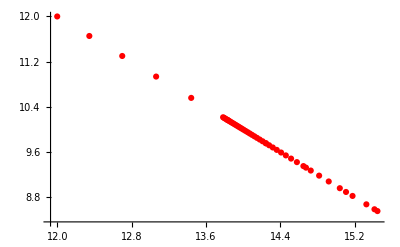

```mathematica
ListPlot[pe2,PlotStyle->Red,ImageSize->Full]
```

```mathematica
pe3=Table[{(i-1)/Length[pe],pe[[i]][[2]]},{i,Length[pe]}]
```

{{0,12.},{1/50,11.6543},{1/25,11.3002},{3/50,10.9356},{2/25,10.558},{1/10,10.1646},{3/25,9.75293},{7/50,9.32281},{4/25,8.89195},{9/50,8.58562},{1/5,8.55344},{11/50,8.67284},{6/25,8.8217},{13/50,8.95867},{7/25,9.07794},{3/10,9.18123},{8/25,9.27123},{17/50,9.35033},{9/25,9.42046},{19/50,9.48315},{2/5,9.53958},{21/50,9.59071},{11/25,9.63731},{23/50,9.68},{12/25,9.7193},{1/2,9.75562},{13/25,9.78933},{27/50,9.82072},{14/25,9.85004},{29/50,9.87752},{3/5,9.90335},{31/50,9.92768},{16/25,9.95066},{33/50,9.97242},{17/25,9.99305},{7/10,10.0127},{18/25,10.0313},{37/50,10.0492},{19/25,10.0662},{39/50,10.0825},{4/5,10.0981},{41/50,10.113},{21/25,10.1274},{43/50,10.1413},{22/25,10.1546},{9/10,10.1675},{23/25,10.1799},{47/50,10.1919},{24/25,10.2035},{49/50,10.2147}}

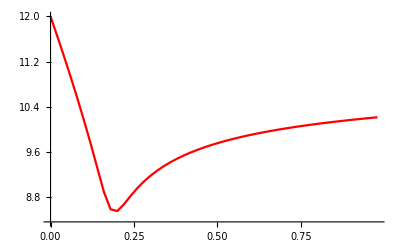

```mathematica
ListLinePlot[pe3,PlotStyle->Red,ImageSize->Full]
```

```mathematica
pp=Table[CharacteristicPolynomial[ca[p],x],{p,0,1,1/12}]
```

Root::deg: (2.-11. ⅈ)-(2.+11. ⅈ) #1-(88.+66. ⅈ) #1^2+(330.-165. ⅈ) #1^4-(0.+220. ⅈ) #1^6-(330.+165. ⅈ) #1^8+(88.-66. ⅈ) #1^10 has fewer than 11 root(s) as a polynomial in #1.

Root::deg: (2.-11. ⅈ)-(2.+11. ⅈ) #1-(88.+66. ⅈ) #1^2+(330.-165. ⅈ) #1^4-(0.+220. ⅈ) #1^6-(330.+165. ⅈ) #1^8+(88.-66. ⅈ) #1^10 has fewer than 12 root(s) as a polynomial in #1.

General::stop: Further output of Root::deg will be suppressed during this calculation.

{5.5178×10^-154 x-5.39889×10^-122 x^2+6.98546×10^-106 x^3-1.22762×10^-90 x^4-1.5645×10^-74 x^5+6.04059×10^-59 x^6+1.77498×10^-44 x^7-2.48452×10^-28 x^8+1.2256×10^-13 x^9+144. x^10-24. x^11+x^12,17+x^12,9,1.66836×10^-158+14+x^12,((0.-0.495064 (-1.05672 Im[Root[(-2.-11. ⅈ)+9+(88.-66. ⅈ) #1^10+((-2.-11. ⅈ)+(2.+11. ⅈ) 1) #1^12&,11]]-1.70975 Re[Root[1&,11]])) (1))/((0.+0.495064 (-1.05672 Im[Root[1]]-1))^11 (Im[1]^2+1^2)^10 (1)^9 2 (1) (-(1)+1)^2 (-((0.+1-1) (1))+1)^2)}
 |  |  |  |

```mathematica
(*minimal Potental Eigenvalue polynomial*)
```

```mathematica
q[x_]=ExpandAll[CharacteristicPolynomial[ca[1/5],x]/x^10//Chop]
```

132.121-24. x+x^2

```mathematica
Discriminant[q[x],x]
```

47.515

```mathematica
x/.NSolve[q[x]==0,x]
```

{8.55344,15.4466}

```mathematica
(*minimal energy polyhedron Polynomial*)
```

```mathematica
ExpandAll[5*pa[x,1/5]/4]
```

(1.234+0.088 ⅈ)+x/4+(1.804-1.672 ⅈ) x^2+(2.31+7.92 ⅈ) x^4+(18.84+0.88 ⅈ) x^6+(4.95-6.6 ⅈ) x^8+(1.1+2.2 ⅈ) x^10+x^12

```mathematica
(*end*)
```

```mathematica
(* Mathematica*)

<<ComputationalGeometry`
pa[x_]=(1.234+0.08800000000000013 ⅈ)+x/4+(1.8040000000000016-1.6720000000000013 ⅈ) x^2+(2.3100000000000036+7.919999999999998 ⅈ) x^4+(18.839999999999996+0.8799999999999891 ⅈ) x^6+(4.9500000000000055-6.600000000000006 ⅈ) x^8+(1.1000000000000008+2.200000000000002 ⅈ) x^10+x^12
pts=Union[{2*Re[x],2*Im[x],1-Abs[x]^2}/(1+Abs[x]^2)/.NSolve[pa[x]==0,x]]
ptsn=Table[Hue[Norm[x/.NSolve[pa[x]==0,x][[i]]]],{i,Length[pts]}];
```

(1.234+0.088 ⅈ)+x/4+(1.804-1.672 ⅈ) x^2+(2.31+7.92 ⅈ) x^4+(18.84+0.88 ⅈ) x^6+(4.95-6.6 ⅈ) x^8+(1.1+2.2 ⅈ) x^10+x^12

{{-0.761698,-0.436509,0.478828},{-0.748618,-0.448975,-0.487844},{-0.702023,0.696324,0.149319},{-0.45614,0.692859,-0.558465},{-0.354324,0.783253,0.510851},{-0.331959,0.931531,-0.148506},{0.274417,-0.81604,0.508699},{0.335787,-0.928559,-0.158193},{0.456284,-0.69273,-0.558508},{0.729263,-0.670641,0.135706},{0.74871,0.448967,-0.48771},{0.766811,0.453067,0.454677}}

```mathematica
a0={Re[x],Im[x]}/.NSolve[pa[x]==0,x]
```

{{-1.4617,-0.876639},{-1.03308,1.5692},{-0.610817,0.605858},{-0.515069,-0.295173},{-0.389855,1.094},{-0.234519,0.518418},{0.18189,-0.54089},{0.398889,-1.10305},{0.527135,0.311455},{0.642124,-0.590506},{1.0335,-1.56906},{1.4615,0.876394}}

```mathematica
(* Voronoi diagram*)
g1=Show[{
DiagramPlot[a0,LabelPoints->False]/._Point:>{},
Graphics[{Red,PointSize[.005],Point[a0]}]
},PlotRange->{{-2,2},{-2,2}},Frame->True,PlotRangeClipping->True,ImageSize->1000]
```

```mathematica
(* 3d projection of polyhedron*)
Show[Graphics3D[{Red,PointSize[0.0375],Point/@pts}],Axes->True]
(* convex hull: MathWorld Library*)
<<ConvexHull`
hull0=ConvexHull3D[pts];
Length[hull0]
hull1=Flatten[Table[If[i≤Length[ptsn],{ptsn[[i]],hull0[[i]]},{Hue[1],hull0[[i]]}],{i,Length[hull0]}]];
```

```mathematica
g1=Graphics3D[hull={Opacity[0.95],hull1},ImageSize->2000,Boxed->False,Background->Black,ViewPoint->{2,2,2}];
```

```mathematica
g2=Show[g1,ViewPoint->Bottom];
```

```mathematica
g3=Show[g1,ViewPoint->-{1.3, -2.4, 2.}];
```

```mathematica
g4=Show[g1,ViewPoint->Right];
```

```mathematica
g5=Show[g1,ViewPoint->Front];
```

```mathematica
g6=Show[g1,ViewPoint->Top];
```

```mathematica
Export["rubber_polyhedron_minimal_energy_Polyhedron_grid.jpg",GraphicsGrid[{{g6,g1,g2}, 
 {g3,g4,g5}},ImageSize->6000]]
```

rubber_polyhedron_minimal_energy_Polyhedron_grid.jpg

```mathematica
Export["rubber_polyhedron_minimal_energy_Polyhedron.jpg",g1]
```

rubber_polyhedron_minimal_energy_Polyhedron.jpg

```mathematica
Export["rubber_polyhedron_minimal_energy_Polyhedron.ply",g1]
```

rubber_polyhedron_minimal_energy_Polyhedron.ply

```mathematica
Export["rubber_polyhedron_minimal_energy_Polyhedron.stl",g1]
```

rubber_polyhedron_minimal_energy_Polyhedron.stl

```mathematica
(* end*)
```